# 2D Nonlinear Systems - Predator/Prey Model

## Predator Prey Model

Consider the system given by 
ẋ = f(x,y)        where   f(x,y) = r x - a x y
ẏ = g(x,y)      where   g(x,y)= b x y - k y
We would like to (1) conduct local analysis, and (2) graph the phase plane to validate our local analysis conclusions.

### Local Analysis

```mathematica
f[x_,y_] = r x - a x y;
g[x_,y_] = b x y - k y;
```

```mathematica
eqPts = Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

{{x→0,y→0},{x→k/b,y→r/a}}

```mathematica
DF[xs_,ys_] = {{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}/.{x->xs,y->ys};
```

```mathematica
For[j = 1,j≤Length[eqPts],j++,
Print[];
Print["==============================================================================================="];
Print["At the equilibrium point ",eqPts[[j]]," the eigensystem is given by ",MatrixForm[Eigensystem[DF[x,y]/.eqPts[[j]]]]];
Print["==============================================================================================="];
Print[];
]
```

===============================================================================================

At the equilibrium point {x→0,y→0} the eigensystem is given by (-k | r
{0,1} | {1,0})

===============================================================================================

===============================================================================================

At the equilibrium point {x→k/b,y→r/a} the eigensystem is given by (-ⅈ √k √r | ⅈ √k √r
{-(ⅈ a √k)/(b √r),1} | {(ⅈ a √k)/(b √r),1})

===============================================================================================

### Comparing the Local Analysis with the Phase Plane for specific parameter values

Let’s first pick some specific parameter values so that we can plot the solution.

```mathematica
parameterVals = {b->1,r->2/3,k->1,a->1}
```

Now, let’s create a loop that iterates over each of the equilibrium points.  We will plot the eigenvectors

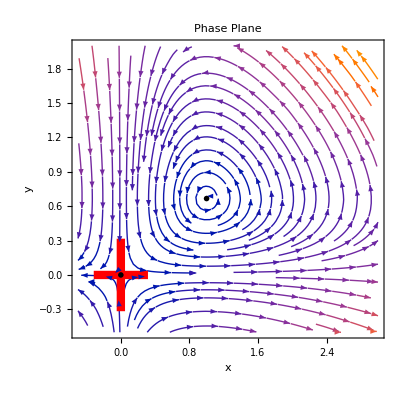

```mathematica
For[j=1,j≤Length[eqPts],j++,
esys = Eigensystem[DF[x,y]/.eqPts[[j]]];
Subscript[evPlots, j]=ParametricPlot[esys[[2]]*s + Table[{x,y}/.eqPts[[j]] /.parameterVals,{k,1,2}],{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{u,v,vx,vy,n},(((u-x)^2+(v -y)^2)/.eqPts[[j]])<.1]]];
EVPlot = Show[Table[Subscript[evPlots, j],{j,1,Length[eqPts]}]];
eqPtsPlot = ListPlot[{x,y}/.eqPts/.parameterVals,
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black];
pplanePlot = StreamPlot[{f[x,y],g[x,y]}/.parameterVals,{x,-.5,3},{y,-.5,2},
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane"];

Show[pplanePlot,EVPlot,eqPtsPlot]
```